```mathematica
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files

```mathematica
superoperatorsChaotic=ToExpression[Import["chaotic/superoperators_1.csv"][[2;;]]];
```

```mathematica
superoperatorsRegular=ToExpression[Import["regular/superoperators_1.csv"][[2;;]]];
```

```mathematica
SeedRandom[342];
ρ=Dyad[RandomQubitState[]]
```

{{0.751454,-0.220224+0.37185 ⅈ},{-0.220224-0.37185 ⅈ,0.248546+0. ⅈ}}

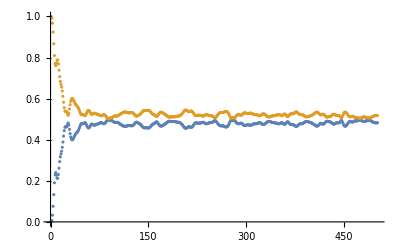

```mathematica
ListPlot[
Transpose[Sort[Chop[Eigenvalues[ArrayReshape[Chop[#.Flatten[ρ]],{2,2}]]]]&/@superoperatorsChaotic],
PlotRange->All
]
```

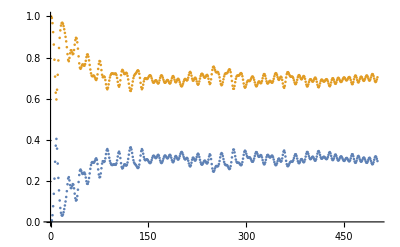

```mathematica
ListPlot[
Transpose[Sort[Chop[Eigenvalues[ArrayReshape[Chop[#.Flatten[ρ]],{2,2}]]]]&/@superoperatorsRegular],
PlotRange->All
]
```

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[…]